# Project Euler Problem 83

```mathematica
mat = Import["C:\\Users\\pfall\\MyStuff\\GitHub\\ProjectEuler\\p083_matrix.txt", "CSV"];
```

```mathematica
rightDownSums[mat_] := Module[{n = Length[mat], sum = mat},
	(* sum along last row/column *)
	Do[sum[[j, n]] += sum[[j+1, n]]; sum[[n, j]] += sum[[j+1, n]], {j, n-1, 1, -1}];
	(* iterate back in square layers from bottom right corner *)
	Do[
		Do[
			sum[[j, k]] += Min[sum[[j+1, k]], sum[[j, k+1]]];
			sum[[k, j]] += Min[sum[[k+1, j]], sum[[k, j+1]]],
			{k, n-1, j+1, -1}
		];
		sum[[j, j]] += Min[sum[[j+1, j]], sum[[j, j+1]]],
		{j, n-1, 1, -1}
	];
	sum
]
```

```mathematica
adjustToNeighborSums[mat_, oldSum_] := Module[{n = Length[mat], sum = oldSum, neighborMin, changeCount = 0},
	Do[
		neighborMin = mat[[j, k]] + Min @@ {
			If[j > 1, sum[[j-1, k]], Nothing],
			If[j < n, sum[[j+1, k]], Nothing],
			If[k > 1, sum[[j, k-1]], Nothing],
			If[k < n, sum[[j, k+1]], Nothing]
		};
		If[neighborMin < sum[[j, k]], sum[[j, k]] = neighborMin; changeCount += 1],	
		{j, n},
		{k, n}
	];
	{sum, changeCount}
]
```

```mathematica
minimalSums[mat_] := Module[{sum = rightDownSums[mat], new, cnt},
	FixedPoint[
		({new, cnt} = adjustToNeighborSums[mat, #]; Print["changed " <> ToString[cnt] <> " entries"]; new)&,
		sum,
		100
	]
]
```

```mathematica
plotShortestPath[sum_] := Module[{n = Length[sum], path, j, k, neighborMin},
	path = ConstantArray[0, {n, n}];
	FixedPoint[
		(
			{j, k} = #;
			path[[j, k]] = 1;
			TakeSmallestBy[{
				{j, k, sum[[j, k]]},
				If[j > 1, {j-1, k, sum[[j-1, k]]}, Nothing],
				If[j < n, {j+1, k, sum[[j+1, k]]}, Nothing],
				If[k > 1, {j, k-1, sum[[j, k-1]]}, Nothing],
				If[k < n, {j, k+1, sum[[j, k+1]]}, Nothing]		
			}, Last, 1][[1, ;; 2]]
		)&,
		{1, 1}
	];
	MatrixPlot[path]
]
```

```mathematica
sum=minimalSums[mat]
```

changed 1390 entries

changed 825 entries

changed 608 entries

changed 551 entries

changed 507 entries

changed 451 entries

changed 408 entries

changed 381 entries

changed 360 entries

changed 353 entries

changed 346 entries

changed 347 entries

changed 349 entries

changed 339 entries

changed 340 entries

changed 328 entries

changed 337 entries

changed 336 entries

changed 334 entries

changed 334 entries

changed 342 entries

changed 334 entries

changed 333 entries

changed 327 entries

changed 315 entries

changed 301 entries

changed 291 entries

changed 291 entries

changed 283 entries

changed 267 entries

changed 259 entries

changed 242 entries

changed 231 entries

changed 221 entries

changed 219 entries

changed 224 entries

changed 230 entries

changed 223 entries

changed 219 entries

changed 220 entries

changed 216 entries

changed 220 entries

changed 217 entries

changed 203 entries

changed 199 entries

changed 204 entries

changed 203 entries

changed 201 entries

changed 201 entries

changed 195 entries

changed 192 entries

changed 189 entries

changed 184 entries

changed 183 entries

changed 186 entries

changed 181 entries

changed 175 entries

changed 171 entries

changed 163 entries

changed 152 entries

changed 143 entries

changed 133 entries

changed 122 entries

changed 121 entries

changed 119 entries

changed 119 entries

changed 116 entries

changed 116 entries

changed 115 entries

changed 112 entries

changed 104 entries

changed 99 entries

changed 86 entries

changed 85 entries

changed 79 entries

changed 80 entries

changed 73 entries

changed 71 entries

changed 61 entries

changed 53 entries

changed 46 entries

changed 37 entries

changed 34 entries

changed 27 entries

changed 21 entries

changed 20 entries

changed 15 entries

changed 17 entries

changed 14 entries

changed 10 entries

changed 5 entries

changed 3 entries

changed 3 entries

changed 0 entries

{{425185,421003,418306,413191,412473,410264,408052,410303,409329,408193,402010,397114,398056,389182,384992,381207,390680,385246,377442,368305,375643,373398,370585,373785,373597,369703,361786,353959,351499,349149,352663,358543,361688,360960,366844,361660,361628,357672,350185,346900,345816,336831,336597,345206,341247,335140,343907,338397,334152,333690,327116,323797,319812,329533,321742,319061,319425,326965,318140,311768,308754,306641,310368,306233,299458,293510,290752,294291,291812,291464,283475,282724,272862,280951,284039,290926,281464,284222,287970,293840},{420740,419644,419624,420777,415207,410040,407398,405955,406250,401372,394342,393838,389594,387246,388282,378455,382042,377429,371546,367809,369012,369964,363433,369430,369045,365336,358713,357893,351745,348458,356439,355299,359097,353327,359645,357877,356562,359244,354236,350686,341891,336071,335725,339659,333196,334006,334371,332647,324436,324319,319497,318180,319537,321543,318745,316363,317538,320442,316657,315967,306989,299519,303318,307219,298495,299382,289533,292188,292299,290373,280740,278576,271599,278182,277638,285058,278296,282483,291836,299916},{430347,427029,420145,422655,416571,416820,407837,400214,398629,395748,388816,394408,387386,382605,378771,376007,375124,372907,372639,367509,361896,371224,362866,364002,365074,359218,360112,357852,353088,346584,352065,346875,351425,345752,352848,351160,355484,363686,355622,345649,346760,341445,333874,334449,331079,327948,330964,324526,325605,324463,323339,313803,315103,315618,310404,311563,317383,316269,317182,308935,307472,298224,299571,302803,294986,293555,288915,288868,285231,285700,278356,271401,271055,279960,275730,275075,277815,282951,287258,290539},{434868,429739,426625,418865,417771,411621,406439,399081,391694,387197,386242,386141,389931,383684,380933,373923,372455,368251,363296,359800,359693,363133,354862,357810,361848,355663,358671,352734,350849,344745,342838,345616,341974,344364,344939,345427,348516,355167,348203,343986,343794,337845,330839,330124,326796,325644,328755,320711,316392,314657,315169,313607,309561,308711,307929,312710,313993,307194,307712,306756,300511,296396,294979,293636,291273,293025,291018,294293,284922,280955,275887,274581,270677,270916,267095,267609,272779,273436,280873,281309},{427662,432135,424165,424577,415507,408130,400448,399134,397976,392869,386559,384663,382154,376718,374986,365506,366002,365831,366049,366619,359244,357037,354731,357789,358312,354879,352873,344733,344944,336463,338673,346005,341264,343244,347397,344712,347003,348793,349391,351376,346542,337844,332940,333152,327403,325578,323538,323398,319416,314511,310351,308151,303110,304598,306866,308041,308673,306592,306208,301273,293961,297145,299309,292556,287488,287577,286473,287408,279502,280524,271274,269699,266436,265873,259222,259567,264345,269497,271617,279122},{424042,424111,423588,414580,413926,408529,403100,402149,398746,399485,390297,386049,383556,382714,374387,364800,370939,365730,359817,359724,357825,357497,354621,351017,358762,352001,346459,338800,336256,335064,340337,341679,335092,336841,340064,340668,350593,350946,346945,346875,339160,332121,329262,326048,333830,326459,328269,324740,323317,316683,315166,306930,300598,304072,306431,309433,301085,298271,298130,296996,292984,291888,290844,290576,284035,284481,284822,288374,279249,274089,265253,260908,258327,264248,255810,261317,261985,265337,266734,273676},{422968,418673,417497,411901,412035,413121,405344,409278,405184,396864,390205,384258,379195,380077,373338,364093,361414,360647,359933,366546,357988,361424,359123,350344,350186,345093,342646,336864,332897,331181,338953,340191,332027,337715,339307,346746,341338,344005,344122,338108,335778,328831,327373,324261,325926,323038,321132,315180,314866,314014,305947,308236,299022,298595,299676,303581,296921,293964,295146,293832,286355,294696,287970,287632,279093,283578,283418,280978,276389,273397,270500,267127,257867,261746,254272,261434,266640,264720,264056,268813},{419823,419313,415757,410380,408974,403253,398307,403410,396251,398467,390174,381893,375542,370630,370343,367473,365362,365969,363773,366402,367551,361296,359390,353092,355614,346655,348943,345699,338111,330250,334629,332232,330910,328471,333524,338970,337492,335143,339111,336523,333954,327054,327914,318253,322435,328399,323050,317052,310264,305020,300028,300254,295027,293569,291988,296772,291918,290836,292637,287195,286245,285725,283988,280285,276113,278889,277075,275567,277228,268127,265628,258737,255598,256559,253230,254672,264665,263488,259500,266136},{429267,421770,419614,413723,404007,402779,395672,395563,392000,392706,386752,382776,377784,379171,375135,367763,365696,364402,361344,361664,367252,364940,359184,349858,353403,348432,343797,344419,338408,330011,328011,331087,328357,326258,329733,335727,333090,328643,333929,327938,329172,321298,319001,317350,317249,320712,318244,309055,302183,296065,295193,294185,292406,300340,291256,287208,293085,288983,288928,285853,286279,285952,281417,274964,271320,277302,278357,273920,268707,271311,264344,254401,248586,256660,250018,256997,266129,261845,254570,258430},{421696,418369,420251,417635,411935,402002,396706,394085,389300,386545,381713,379201,377083,374839,370432,368262,373228,368425,360038,363910,358371,359898,352974,349447,344753,339608,338302,336137,330197,335135,326783,323270,326768,319785,326162,330466,336376,327344,333159,327395,323686,320340,319370,324893,315156,319583,319280,311317,308707,300271,294705,292728,289601,291534,293388,285085,290451,292353,286078,284116,276820,281880,283122,273978,271212,276753,274971,273229,267367,267309,259690,252125,247917,254003,248180,251571,257570,252530,253855,253382},{421221,414339,413074,411299,407651,402961,402543,397837,393317,387923,390046,380561,379435,375417,379606,371194,368573,358683,354987,356223,357401,362112,352757,345694,344100,345810,342128,335714,327772,326225,326485,321361,325891,319439,320449,328208,327046,320141,326554,324329,328473,321931,326268,317788,309345,317616,309341,307624,309051,302218,295862,289000,287202,287549,286880,282593,290575,282551,276885,284040,275787,279207,275699,274506,270061,269124,269802,267234,267730,260049,254147,248724,246204,247724,244971,246663,248346,245121,253515,244842},{423342,417762,417797,415032,408499,411002,410464,405662,397385,393291,395306,388054,385140,376432,374449,374827,368702,360609,354871,354500,359920,356935,347879,351298,342182,337236,334534,329491,329921,320059,318597,321007,318959,314788,322296,325333,327002,319480,318865,318237,319181,318086,316663,312310,308902,309381,304178,299904,301786,297146,288083,293819,285448,282324,280219,281413,286241,281514,276797,274887,273947,276522,274862,270351,267413,265586,263559,260859,259623,258782,253022,251342,245082,242709,238858,237804,238976,244155,245147,242400},{416004,415108,415298,411738,414564,410504,412310,402987,401364,397672,388800,379202,375974,374182,371648,370947,361655,360022,350833,344692,352561,347441,347278,344910,339925,337218,328961,326570,324561,322321,317328,325341,315506,312079,320491,319092,322784,324969,316458,310037,314992,312594,311014,304957,306312,306068,305774,299194,294457,288601,287127,288270,281726,278071,275434,283475,283242,278070,272249,278509,272964,280419,276951,275354,275537,267124,263478,268819,263497,257389,253751,246752,243316,241875,237017,232836,241567,241800,237972,238891},{411584,413781,415368,409362,408304,407516,402773,398923,396535,390456,383994,381179,375559,367064,361686,361611,357287,353846,343976,342863,342698,341154,339975,337141,338194,332018,332103,329425,320586,318558,314260,316276,313665,311738,317719,316958,318750,320336,314894,306996,305980,309611,303725,304857,306500,298164,296588,292274,289165,286593,280582,279939,279836,273060,274595,277993,273987,271546,268387,269721,272902,278746,273438,277738,267840,263206,261402,267832,265898,262349,255853,251307,249802,242998,240391,230970,233873,234055,234228,237891},{411228,405485,407043,408656,407027,406886,402275,398384,401129,394893,389685,390838,382955,374578,364853,359803,354460,351921,345820,352563,350448,349268,341936,336579,338535,329705,325267,327145,317600,309104,309061,309388,315269,305872,308959,316638,319222,312040,308374,300875,298739,303946,297911,302042,306610,298971,296519,297660,292590,282887,278496,270878,270433,269113,269108,268262,266706,269898,266568,274847,270263,273965,268324,268280,264656,260675,256990,263152,261636,253867,257269,248433,250240,240802,236635,230284,225224,225195,226434,231219},{401358,405333,409098,403693,398277,402132,395754,392128,392311,393874,391602,382089,380608,377779,372424,363121,353967,359063,352409,355419,348991,342655,339116,333578,338416,331770,325068,318802,316043,311435,306983,316389,309994,305766,302869,308457,310576,305626,303816,295425,293889,297673,292897,298079,300412,295058,289948,289126,284172,282194,281421,275741,272688,271753,267214,261491,259323,260707,261860,265141,263324,266028,259598,258898,259440,260445,254743,254123,253482,252129,247285,245807,246476,244939,235830,229569,228447,223977,232470,233314},{401166,400120,400801,394719,394245,395166,390037,390949,385788,389195,392214,386196,377567,375327,367342,357593,352578,350361,349366,347601,351074,343422,337023,330484,334864,326763,323086,326779,317167,309245,306366,307817,301930,299387,302425,302855,306409,311556,307193,300957,293573,288959,291719,301319,294549,292439,284576,286192,285843,279223,279155,281882,274684,267123,265355,260216,258785,259015,260541,257601,262884,259849,253332,251186,252055,261457,254919,254862,250346,244779,251284,242652,243656,242921,233417,235308,228538,223963,230433,237300},{400478,395819,400770,398615,389271,387344,387935,389327,380616,382249,384140,376480,370981,365365,361622,355821,358474,352774,343978,343199,345848,341299,333161,329135,328360,324190,321758,317584,321377,314152,306135,303302,299275,298879,298068,297891,307700,306158,307606,298407,289903,288679,288626,292145,295851,287869,281945,279566,279258,283141,277844,276978,272142,269799,261935,261130,258564,265440,259994,256633,261245,257557,252820,249540,257433,255956,247851,246217,243288,243014,241594,238500,240730,239276,230478,227804,222464,221019,225604,229441},{400842,395083,401732,394288,388815,381073,379098,382214,377375,375670,378420,371359,374787,365915,360512,351139,348726,347513,348167,341366,343746,342025,339322,336013,330376,322045,319535,313843,313837,308772,303710,300871,300289,303306,295197,296741,298310,303439,301926,293982,294259,288139,286575,289549,288081,280502,279184,279972,275900,276636,275794,274245,267052,263455,267052,261203,256155,260694,256880,248011,255673,251662,250182,249099,250400,253807,253787,250592,244720,239088,233808,232377,232497,229355,229036,226001,225018,220816,222464,226750},{396316,394745,394919,386320,385090,377318,377507,385613,376564,375020,372695,368898,365557,356524,356958,353487,353416,347082,340366,336372,343558,342458,337344,333734,326067,319507,313442,312568,315080,310483,310871,304359,299548,297395,291672,296688,303131,294817,296713,291077,297635,290600,284736,283979,288815,286416,276507,274715,271482,271035,267859,266589,261860,261591,261166,255120,250575,254492,253799,246375,247766,246903,241100,243245,247215,246176,246933,246993,244634,239228,234396,230300,222780,221924,224780,217740,215338,216329,217712,223675},{395139,393317,391607,385650,382965,373097,368984,378337,372522,366294,365128,362162,360075,354420,352079,348520,352812,345472,344499,335103,334563,335919,340671,331136,327486,324109,316526,311720,310679,310911,306061,301286,292814,294789,285316,290662,293948,292231,291142,289985,289856,282677,275989,277092,281310,277552,277468,275446,266956,273902,266351,258546,261140,256379,259189,250132,249866,249215,245543,242733,248984,243855,239632,245191,246746,239875,239166,245918,236147,229457,225611,225094,227943,220319,215808,216120,212952,220361,218824,226951},{397231,388493,388694,379139,375444,371061,368683,371308,369025,363413,364752,355206,350951,344846,342846,346919,354572,345615,336593,334748,329816,327329,335828,327986,320153,318968,314805,308127,307941,302754,300846,295084,290530,289039,281410,283680,288443,286178,283206,283911,288458,281853,274425,276815,274450,271713,276899,270931,266046,268392,260728,257665,254116,254524,249741,245342,248592,251733,248277,241959,241361,241258,234782,239120,236771,234940,237251,241675,233683,235906,231268,224631,224416,215916,215194,209726,209291,213230,217429,219404},{391690,384643,380320,378386,373223,369057,368596,365052,362285,355731,360511,354413,352148,343070,340995,346110,345654,339229,330046,329559,334592,327026,326226,324251,318525,315605,312762,304983,299352,295658,291933,289261,285640,281360,280198,274386,282559,286172,280194,280552,280664,275061,272846,272465,267204,267412,269120,263141,262752,258845,256361,258091,252158,246287,242983,241845,246959,254567,245368,240296,240653,233544,228639,232230,233343,228087,227917,233953,233092,230049,221482,223219,222447,217987,210681,208355,209183,211711,213423,216869},{387073,383098,382001,373984,369766,368840,372082,369067,364675,355528,355517,356633,350990,341345,336351,339469,337242,331849,336696,329458,329240,321404,328720,322752,317416,310231,306942,305288,295599,297544,291807,288404,287280,284601,281789,274041,276058,276387,278669,279597,284965,275884,270266,269408,264439,264422,270457,264835,259254,257310,255129,254190,253775,254787,248482,240229,245296,247557,240713,232854,233408,227072,223879,225871,224290,220211,225353,224549,230419,221023,219221,219845,222678,213699,209864,207389,214811,208437,216782,220761},{387477,378533,373870,368184,365196,366534,363244,365820,356679,356281,351606,349515,342067,342777,334323,333407,331811,329570,327944,326800,324059,320410,323666,317592,310422,307519,305044,299719,293268,292344,289016,288494,292093,293319,283582,274025,273334,270946,272029,270229,279435,271296,274343,273118,270423,262319,266652,256792,251779,258738,260812,256067,256293,252114,244342,238074,237453,239583,236850,231108,233916,224333,221262,217135,222118,213887,218708,215658,223004,215501,213118,217988,220995,215233,215050,206079,210071,207827,208843,213146},{378229,373136,372998,368359,361750,362175,356610,359153,356182,347105,344833,343859,340160,337695,335045,338172,333174,329607,326560,325639,322903,315048,314875,312810,308572,307524,311891,309267,301900,301538,294958,292259,293449,292813,285588,279309,272056,269563,268008,268620,272789,266589,269143,266011,266615,257986,258340,258610,250555,258194,252285,259449,251748,249969,242405,237561,232538,230234,230880,230402,227447,226359,222558,216355,214607,210870,209594,211822,218301,219693,211141,214062,212960,212854,205346,205042,211325,204185,213320,216266},{383755,377518,376632,369105,360604,360530,356515,351632,349092,349633,344772,339471,337901,337480,337204,337731,339811,333822,328961,333161,328711,324419,317469,312171,310126,309452,310886,306407,306569,300089,291560,287482,285539,283842,282078,276625,269540,268580,266175,265436,263336,257536,262246,258203,258802,253109,256469,252102,245674,251809,250748,253069,249240,243383,236560,237433,233324,224838,227687,228868,232643,225192,226772,219752,219929,216501,209581,207702,210586,213572,208094,217110,219125,213116,206824,203762,206136,201618,206237,211000},{379220,372911,369448,360058,360082,353159,357542,352930,343225,343267,342236,344598,345277,340371,333843,338784,336173,334995,327106,329542,326906,330150,322788,313630,305030,304005,303131,301292,299509,299200,290170,288327,293644,285246,283813,276695,277611,271457,270079,272396,263530,256808,252509,252499,257575,251678,247490,246890,245001,244269,250742,245296,245579,242506,236410,231564,228416,224154,221871,219242,226327,219613,218512,228488,218503,218420,213753,205575,207856,210220,203117,210896,214256,210456,207358,198091,200168,201540,203420,212970},{369315,365784,362642,354873,357642,349438,348378,345909,338884,344693,341190,342517,344670,339696,330595,336575,336592,328714,323742,325056,321548,320748,320122,313816,311825,304515,306457,301073,300387,296400,298821,290179,286938,284195,280394,284283,275695,273422,273354,266364,266222,263025,256187,250570,258913,255965,256136,250370,241676,241784,246653,240822,238135,235514,233495,225398,223975,228025,219811,214890,218552,221859,216298,224569,218288,210150,204003,202835,199495,203225,197187,202232,204566,202154,200458,197747,207314,205683,208248,209951},{363490,357267,355168,352468,357184,353108,344775,343413,338406,336359,339193,338825,337237,331492,323301,329077,327177,323262,319892,321662,314691,311535,313315,309404,306916,303661,308047,300864,295409,295508,294941,288524,285134,283769,276581,276520,268994,269006,268038,259874,266298,257599,249684,250456,252922,250121,248524,245215,241611,240993,240674,246049,245667,236788,228441,229976,220331,218261,216706,211624,216864,218886,213822,217778,210265,211351,207479,201309,197497,193351,190615,192359,197907,196545,198011,193816,198859,205476,200415,201064},{363937,359940,358603,351879,356834,347526,347680,342312,335653,333511,334752,330428,330045,324879,318385,319122,321101,321283,313496,319644,315438,311287,311470,310320,301986,301203,305987,297464,295239,288699,293816,291226,283178,277415,276004,271056,266791,272269,267483,259395,258779,258778,249177,244063,248290,249505,240990,243978,244925,237713,234613,236256,236429,232795,227873,222451,221108,213063,210224,206624,207652,212231,207861,217328,208942,209282,207432,202916,204733,197682,190548,189208,196540,193764,188332,186252,193855,196889,198522,196533},{358111,356250,354637,349758,347874,340540,339574,341357,333992,331869,327582,327551,324288,319562,310359,312551,312714,311322,307453,309886,305831,304837,302839,304587,294627,295947,299142,297380,287752,286722,284261,283793,281394,275001,275439,268472,264364,263291,260481,250554,249571,249833,243367,234665,239424,240367,236814,238103,239015,234441,227854,230578,228780,231971,230757,222434,212911,209909,209205,205937,212546,207804,205777,209015,204450,202020,200136,196378,197076,195485,188471,187703,190164,186874,179368,181373,190223,189489,192549,195794},{362163,362937,359342,357018,350934,344289,337574,333868,335822,328963,326110,329725,321538,313335,309319,308448,306639,305273,307123,300633,301769,300569,301204,295963,294050,297891,296136,297482,290031,282630,279282,277319,280774,272202,268956,259785,256640,255899,257428,248469,246371,244721,242371,234400,231778,231702,228828,230837,236978,228788,227242,229955,228076,229954,231152,230395,221516,211556,204141,201977,204337,207213,203019,200622,199575,197379,190552,189977,189193,192955,189436,187260,184674,184215,177516,180677,182301,183713,188062,191525},{362613,357984,357918,353658,345526,337934,334753,328364,327150,326884,324974,322523,313739,310949,313524,306900,307281,300321,297829,295294,294897,297924,295121,288089,290994,292673,288651,288686,285322,279621,277179,276893,277564,268039,263211,256609,255692,248245,248084,245252,247175,239141,240833,236448,235689,234906,227948,228803,227049,233551,224583,224144,224322,222858,223716,220701,216700,211651,206290,201024,206538,213705,210935,207309,206513,197999,190858,196087,186518,184134,182634,179288,178678,179925,175382,173100,179414,183915,188889,187145},{364066,355750,351678,349653,342769,339742,340467,335988,335030,335412,329179,326095,317409,309822,306592,305453,298295,299339,292353,301662,294008,296839,287480,283006,285218,292520,288466,293525,288438,280906,274339,272733,275384,266403,260791,253995,249610,244534,243579,237507,240636,232627,235926,233843,227936,229291,220678,221867,224043,225180,225808,221818,219670,219773,220291,210838,212318,206712,197602,200727,198958,204928,210545,202210,197830,192202,190798,189481,191826,187245,180749,174687,171349,170885,169285,170373,178605,186344,192590,184316},{358614,356273,358774,358050,351070,346283,344877,335033,334789,329796,327516,319827,315802,311606,306084,298180,292132,297697,288439,295608,292544,291243,283156,275911,284251,288827,285883,284063,282049,277031,273610,268297,272806,268879,264875,255081,246712,242527,241039,233829,232305,231289,232670,224998,223153,224642,216607,220635,218015,223004,222698,223440,215922,221078,211485,210300,205573,199548,196676,198347,198485,201250,201817,195138,188768,194526,192988,184342,181964,189363,183864,184377,179576,170699,166753,175546,175195,181518,184459,180443},{365044,358679,360426,351432,351376,350109,351555,342112,336034,328455,323223,316532,313097,306379,300681,296537,289509,288917,286290,286147,286096,284505,283112,273994,276634,281700,277417,278338,275053,274359,271162,267785,263642,259042,259460,251423,247079,243181,241607,238023,233734,226669,223235,222520,215388,217011,215910,213958,214291,216016,216845,215778,212027,217530,214901,208116,200179,193814,189011,195277,200958,192781,195069,188679,188207,186591,193615,187528,181502,181608,186775,181993,180327,172177,164025,168500,174951,179801,175793,176172},{364531,361721,360767,353008,351267,348992,348672,340996,332356,328239,326281,318781,310733,308976,305022,295752,293781,288985,286073,285413,279902,276349,279693,273936,274669,273631,273290,279065,282779,276769,271088,268429,258840,255718,251326,244470,239454,239583,239697,240726,234090,228477,221129,218530,209586,209091,206850,206427,210970,216719,216342,219379,211583,214026,211802,206107,197931,195942,188813,190158,198850,191311,190957,187073,185303,179036,183781,178861,179469,179885,184522,180624,171781,165131,163552,172818,169047,171854,172731,172891},{370737,369973,362325,356397,350560,346383,342050,344578,337937,337409,327883,318977,317479,309068,306084,300886,296245,297420,294587,287887,279213,275337,274738,269411,268585,266433,264938,274265,275483,268178,263378,260650,257042,253193,250511,248648,238705,237298,236341,233244,224134,224232,222229,218118,211573,205629,203272,205876,207879,209512,209173,214641,210336,209748,204886,200142,194189,187557,186503,195376,196930,188644,186389,185693,176984,175451,181412,174971,174541,172542,179137,170852,163834,156345,161496,165237,165593,169190,172133,170231},{365136,365771,359783,354339,347114,344789,341843,336644,336175,330725,323217,328892,321864,313580,305597,299256,295980,292659,292643,291322,283714,278699,283229,276135,269167,262349,262505,265080,265786,272536,265425,260565,257424,249332,247013,238914,243258,233307,229150,228151,218468,215798,217525,214669,213601,204848,202109,200881,198260,202758,204973,204959,203682,205892,204591,198879,194604,196087,186210,185937,189074,187170,188206,181519,182161,173607,181557,178140,175075,166479,169706,164686,155777,153425,155230,158438,167194,172483,168109,163566},{361289,359415,351242,348104,349647,349104,344212,340895,338692,328993,321020,322955,322251,320228,314525,304911,303226,293634,298547,289429,289742,286947,280484,273574,270112,261552,262970,266998,270375,263020,260081,255108,248214,244281,240497,237297,234878,225644,220897,218689,216482,214537,212815,214217,208072,200049,205737,202671,194985,196570,200274,203168,194164,197191,198659,197243,188593,187703,183277,181755,183015,184240,181793,174837,172390,172953,172120,176714,167225,164652,164235,160068,160111,153302,150836,157961,160720,166970,161192,161510},{355831,357592,351592,344814,345077,352827,344545,341943,332155,325350,319857,322680,316774,314801,305628,302520,303349,298812,291681,287235,282420,278772,272071,271312,268000,259645,255160,260348,269094,266921,259162,255634,253457,252660,244335,243634,239438,234831,228011,220795,218605,211638,211408,209829,201919,196565,205523,199197,192248,192742,201495,195972,188974,187451,190016,189763,183235,189003,189895,180048,179402,174353,176015,174888,169628,173684,170671,172717,167851,163572,164112,156612,164894,155127,150609,160291,169254,160725,154720,153421},{352565,350567,341836,340900,343812,343711,336822,332737,332646,324901,317765,313992,310182,309452,301197,298492,297342,293690,288402,286068,286484,277140,274472,270782,268754,259075,250973,255291,261772,264245,260695,255762,250181,247939,243954,236401,235366,231446,224016,220071,212432,208718,205326,202801,197806,192956,196602,194184,184517,193819,197153,187265,187742,183025,186473,182678,182588,182232,180749,181886,179755,173529,167598,170939,166898,167982,168158,163442,163825,160805,155428,155447,154991,152564,150554,155067,161539,160089,152618,146898},{351628,342750,341137,339421,338553,336647,333966,333402,333370,327375,324920,317424,319673,313776,304689,295839,287552,286883,286060,285713,279519,277255,277114,270391,263734,255226,250399,252487,257147,255070,255272,247700,247314,238282,237343,232959,240484,236132,227713,222157,213094,217605,208760,201734,193200,190089,188651,190903,184031,184313,190342,186484,178876,181323,186386,183348,187442,181981,176549,180313,172786,171050,167112,164059,162494,167789,162989,158532,157258,152470,150742,150404,152377,149212,147887,154313,155770,152868,147023,145282},{352876,349239,347833,342931,347292,338237,341790,339387,330744,325956,327976,320926,314740,307760,298395,288613,288422,289380,288136,279638,277420,274663,269243,262775,262189,258869,249639,249811,254202,250189,252662,243889,252353,244916,236874,232030,236465,232077,231289,224458,221880,214879,208404,200031,197872,188635,186569,183305,178305,177626,180695,182876,178803,178309,183821,184783,183615,176350,173182,170517,164311,163142,162039,163558,157486,163776,160503,161006,155680,158127,154765,149804,143962,140677,138536,146563,148883,156512,150058,145157},{353377,344880,338199,333467,340527,335824,338900,329870,323212,322379,323609,315934,312727,302931,293645,288732,293540,295234,287584,278249,277440,273765,271168,266024,262079,256989,248605,248418,244316,245117,243271,242711,246840,239295,230005,229955,228190,228476,223574,214988,213231,213035,207308,199453,197450,198532,192480,190769,182139,177271,183271,188358,180838,176001,181806,180449,174177,167564,164545,160743,169892,161193,155445,162541,153216,154618,152587,155254,148886,148736,148464,148498,147220,143374,134638,141113,144573,147691,142979,143850},{349395,343871,335862,326316,335088,330620,332559,322713,323411,317365,314886,313932,305807,298765,297221,291062,289625,288982,288099,282224,275376,278255,270188,268126,264926,257631,258110,249992,243056,242672,240479,238289,238451,236310,230807,234049,226669,221555,219309,210620,211666,207912,208576,199314,192616,189600,191753,184816,177069,175941,175579,180801,172858,169973,177036,171359,165912,165859,162960,160045,169066,162981,153480,152883,148799,148624,147003,147028,145949,148533,142721,151284,141522,134889,132043,138771,139231,141095,141830,136930},{341207,337076,328283,320006,329548,328120,324558,316121,316539,313508,313579,307493,300418,300099,302577,294645,291545,284378,280200,282725,275005,277589,275932,268045,261686,255774,254294,252944,244415,244499,242486,237988,229916,239343,229345,234940,226136,216731,210476,208857,206692,199201,201419,195995,188617,186955,186452,180694,176585,173008,172023,174775,174909,166851,167931,170319,165494,163010,157812,156346,160850,157021,153691,149285,155149,147978,147002,149075,139882,148354,138395,141370,139061,129495,127810,132730,130147,139966,135967,135705},{331272,329020,319166,318181,320372,319874,318256,312790,307411,303833,310686,312006,304146,306450,304926,297779,295087,288166,278474,277617,274310,269312,271726,267403,263472,254055,251514,245215,245202,244779,247412,238281,228787,236798,228198,228806,220387,213139,210479,207870,199291,199200,192537,192955,185280,188066,184102,182666,182273,172628,168823,167160,167711,161819,168995,163909,158621,157514,157978,153934,150965,151117,152279,145680,146379,143617,140797,142379,138345,138651,138181,134110,134583,137343,127710,131229,123009,131169,130330,134729},{327806,326801,322289,317103,313150,310986,315083,311237,307990,299293,306369,303316,307187,304797,298006,294787,292368,287738,282583,274754,273274,267140,265943,273159,264236,255449,259086,250234,249207,242680,239184,234476,227891,229099,226555,221877,220767,217270,210580,202774,201552,195301,187031,186610,183333,181901,179816,180731,183460,174401,172187,165704,158858,156114,159106,156420,160865,157131,158056,151624,147622,152168,144474,140700,136450,138584,139060,132426,131148,129493,137049,132786,135497,127667,123726,121549,119403,126482,122946,129297},{334319,327039,321897,317636,314831,307614,312325,310949,301733,296271,296473,299215,304440,298668,299526,292045,288290,280771,276447,268763,272874,269910,264529,268160,264005,260580,252733,251120,241439,237533,231180,225651,222829,219474,218567,221032,216775,209286,200614,196258,196220,195506,188930,182887,182964,177071,172881,172636,176681,174120,167110,159409,155738,154527,152905,149729,151769,147504,151385,148358,144127,142229,136766,133235,130571,131625,132621,129185,127747,127138,127988,130175,127890,125274,123725,120260,114314,123587,122427,129862},{327970,318453,318054,314805,312209,304473,302331,301009,301432,294082,292468,292273,294592,293318,291466,285380,283719,278647,276065,268106,263421,260614,261585,261317,256506,254977,251005,242289,239655,236354,232942,224321,223578,215577,210843,218587,212979,204887,201216,192275,194272,188614,181515,178734,178635,176703,172260,170900,173916,164588,164183,158655,156666,155175,151685,145205,142452,139704,145747,141714,137184,144614,135385,130414,129224,125667,132849,134176,124748,126144,132956,126044,133831,127344,128328,120839,113624,123561,115473,121871},{326666,319222,323184,313496,312864,311293,308784,300041,295703,295366,292000,288927,291327,286096,286013,285388,278402,278153,274202,271042,264243,257697,260548,255619,258226,251264,247016,243235,240345,239195,232677,225983,221638,217911,209955,213732,210564,201912,200175,190788,195974,190053,186819,183928,184436,175786,167504,166248,165145,163007,156328,154343,150690,147920,145487,141209,140594,137731,136016,138184,134394,135197,128199,125111,127350,125316,130727,127558,123406,117124,125357,124652,125527,126764,119190,116203,111616,118382,114367,114761},{322428,322238,319493,315874,316233,310185,304344,298921,298364,295464,295092,286981,283108,285992,281803,284532,280133,273092,265509,263082,260218,256693,251691,249622,248874,246926,240911,238227,237789,237019,229129,227466,219579,211820,209935,209778,202008,197488,192610,188753,187616,184091,188435,182159,176590,168941,172037,172440,164597,166308,163956,163103,160131,151520,150828,143597,146234,144870,135774,134816,131758,136263,131590,123440,126284,124359,130643,122963,122414,114243,115383,122251,126317,119221,116589,117661,108469,113928,104482,111796},{319141,319597,316634,309056,307160,304065,302736,300624,297990,293449,288926,284556,281794,282131,279957,282946,276059,278174,269707,267362,269310,265549,260526,255079,250777,248704,245786,240029,237031,228652,230857,228601,225978,219160,215203,206829,200534,196987,195510,194973,188175,181041,187405,180927,171068,168037,168033,166531,162398,160660,158853,154028,160371,157458,154080,153419,152902,147369,139288,133924,131174,130364,124046,122259,116668,123261,122481,116144,122585,112724,118096,114586,117516,119605,115290,112427,107762,103973,101772,105724},{317369,318096,312123,305515,308195,302577,295710,298051,291975,288816,288028,284888,280144,285613,279048,274788,273137,270703,267326,273911,270411,274561,265940,256119,247987,240130,236044,234975,227484,224496,222917,220475,216154,214005,206363,200255,201749,195663,192496,197797,188269,180606,177921,179812,170616,173147,167600,166023,164884,159724,159680,153565,154083,147757,145574,149275,143347,138681,131120,130457,127940,124187,129959,125409,116249,117745,114507,107658,113046,106343,111338,114392,114455,116019,114463,112009,108937,108977,100280,101308},{317243,309169,308078,299833,299209,302701,293995,300420,291677,291368,295196,287766,279314,276360,273236,269767,265521,262169,265780,264321,271753,270127,267109,258918,251741,246116,238996,241900,233019,225326,227497,228703,222574,213115,204504,200005,198826,193838,192472,191922,189662,183573,176701,176432,169219,167371,170965,164293,159403,158747,159902,153366,151540,146797,141807,143972,137761,135441,131538,121808,118252,123238,124715,122630,114379,111981,104620,103181,109730,104930,111443,108898,107324,113827,105494,104871,104940,106774,99634,101268},{315283,307438,302744,302857,294608,294318,293840,291529,291780,289304,286988,282721,280609,280339,276532,273507,265918,261064,261271,255644,261852,265711,259243,249635,251555,244485,239738,235556,232698,229932,227071,223239,220963,219913,211345,202292,198048,192444,192342,189586,188859,182972,180406,172484,172440,166454,165833,164631,164257,157269,153828,150201,152080,145199,140631,139233,130554,130157,126229,117070,116703,122830,119773,113985,110681,102552,103675,101006,106884,101872,106350,107697,100336,107645,102088,99626,99509,100273,92549,94861},{308015,303851,300214,298214,297273,288370,288331,289941,285840,284809,281122,277700,275983,278875,274360,271573,265446,259066,260723,251718,253506,259199,249954,247717,246791,244086,244792,241109,238710,228903,220802,219132,211981,216263,216431,209122,203834,198180,197860,190554,187844,184810,186771,178802,176950,169038,167913,167281,159844,153139,150885,143457,142637,150109,145527,138027,134185,133755,125692,120452,113786,118351,120449,114391,111531,101641,102499,99543,97135,101608,103309,98757,99227,105418,105131,100204,94817,95470,92324,95324},{312020,307762,300882,299186,295604,289811,284888,282769,289129,284908,276221,269618,271038,275385,267156,262263,256097,249531,250783,251500,254699,260268,252917,246176,241121,237548,238745,236408,230808,227889,218877,210418,211536,207931,217237,211825,209720,205423,203584,196414,191647,190184,185733,182080,174909,176040,172870,164150,156311,151778,150107,149629,141855,140248,137931,142636,139869,131983,127423,120663,113392,115581,112584,109496,101821,95613,96382,94819,87979,97612,101111,98155,105458,100145,100500,99670,93933,93968,90346,95575},{319138,311284,310037,302742,299675,290863,283816,281614,280073,275210,270610,265850,265524,265458,257547,257467,253724,244995,245798,246566,246623,251206,246298,240013,233722,232986,240452,234764,230632,221931,214397,209110,205464,206706,209048,203007,211042,202287,196219,187622,185640,180928,179034,176915,170679,169209,168794,165757,159920,152222,154688,146873,145644,138372,132494,139272,133862,127223,123634,118624,110311,113552,110101,107722,99320,92512,89561,93052,87857,90047,96211,96088,96912,95596,98409,92482,88328,85369,83588,91844},{313219,306041,305016,300597,299853,291541,289774,282919,274080,273761,270799,265137,265090,258783,250121,250053,245240,244673,248537,238606,239060,247152,245689,241186,236253,229597,231113,233726,231337,225081,218720,214857,204872,203641,201466,200415,207822,198078,195190,186025,179858,181194,176134,173372,166640,162640,168216,165203,157450,151522,151361,144382,142030,136402,129411,136425,128358,126554,119934,116156,107730,106935,104232,103177,97528,96137,87240,96906,87360,88448,90024,94746,97598,91143,90669,90530,93587,84040,82106,85833},{310952,303995,300884,300858,293328,286185,284890,283146,277089,275615,278640,270542,265891,263657,259568,252673,251264,241961,244338,236928,235959,238925,239156,236808,235560,229505,225267,228946,228052,220865,220175,210195,206621,203661,194288,197381,198630,191923,187972,178238,174022,171876,168274,163728,157699,156160,158773,157015,153355,152263,150733,144008,136768,130023,128213,130355,122491,128118,122830,113478,104736,103813,101108,96842,93610,91346,84585,87236,86726,92575,92386,85811,90343,91668,82503,83113,85625,81154,76546,81991},{313070,308653,301897,302783,293986,294994,289922,291849,284002,276461,276819,273462,275219,265402,264174,254194,246601,241934,238847,239137,235919,237917,233508,229212,226923,227423,222124,227364,224029,220497,212283,203110,198907,196636,188656,189855,193200,189048,180649,177181,175405,172217,162903,161183,154660,151727,153918,152864,151906,148887,142724,139280,129741,125421,125266,121274,118446,119694,113623,113099,110204,105837,97774,96564,98155,89084,84222,92360,83343,84805,85656,77955,83003,81989,80345,83620,87113,77781,75636,75750},{319904,310620,306817,302619,300692,299338,297305,292619,287833,277943,275933,270705,269481,266323,267198,261154,252164,243281,238068,237992,229686,232349,230360,228898,224269,219525,217103,217903,218436,212658,203528,202211,199115,189491,185673,183903,183208,180754,180297,177171,180628,170690,167163,161467,158830,151106,145233,147381,142920,146310,141547,133854,129723,130597,123002,120502,116296,125426,122137,119607,112591,105190,100799,93216,91829,87760,83739,85400,79246,78619,75841,74345,80701,83657,79342,73755,81986,76882,73692,73537},{317470,316177,308605,309422,302828,300520,293676,292096,294032,287857,279662,269663,268213,259356,258618,260754,252185,245506,244112,236273,227655,227369,224721,219379,217085,213880,209334,214644,210359,209400,207170,202258,195502,189568,192705,187878,189249,179807,174268,173697,173933,168059,162613,156707,152384,143368,142385,140939,137153,139465,133224,134514,126864,126369,124820,115687,112636,118192,113557,112978,104360,101813,92430,89772,93375,90741,83183,84688,80833,81563,75072,70139,79877,75223,70851,69939,74210,74435,68117,72522},{313683,311033,307150,302996,297187,298551,291715,287285,285497,281046,279415,272954,265724,259707,253956,253818,253230,247948,252149,243039,234004,227731,225216,223646,217524,213332,209158,205939,206618,203266,198846,194237,188498,184363,187549,181241,184739,177303,168684,168878,169223,162252,154024,149836,148344,148675,140627,141098,135634,133498,133039,126116,129854,122999,116577,115630,108087,108518,106246,103240,101044,93724,90486,86996,83894,83857,82564,80745,77509,80112,73565,69986,75551,70600,73398,66344,66439,66496,66898,73538},{311913,308812,307755,300698,296872,290795,289770,286815,286167,285903,279174,275858,271963,266910,263379,254629,256301,251884,245198,243772,236831,228760,230201,227357,218347,212225,205628,204006,202432,198919,197235,190149,184644,181400,189718,180080,175930,175023,165888,165059,164078,166672,162805,157186,147435,147430,138299,134326,127167,125827,123971,123890,122275,117719,109521,107588,104791,107139,108373,110984,108968,101911,93265,94539,85860,82899,79352,75978,72468,71339,67771,65530,69377,63321,68673,63509,59386,57408,66108,69102},{315470,318724,310856,302818,294580,293798,293790,285591,285053,280552,273272,271160,268673,265047,262257,252825,256302,252574,245013,240186,237968,235892,230444,221692,220224,212753,206367,212768,209524,201201,193081,196217,190047,180989,187019,188067,184515,179766,171235,171683,162371,161313,157042,158125,152839,150968,144043,135437,126233,118872,116457,115897,115311,111309,108665,106738,103914,103146,103920,102964,99619,98617,97809,95585,92490,87762,87995,79364,81421,75163,67843,62905,60239,57347,60467,55840,51708,55575,57441,64622},{310605,314376,311542,304408,295481,290703,287790,284464,282460,279371,271518,270140,268411,263634,260928,251350,249990,244297,241261,239410,232162,229759,235627,228193,222582,213366,216038,209187,202056,194337,187912,187139,186422,177619,177459,182061,178746,171549,171160,166647,166807,160416,155883,159875,155649,146939,140312,139668,130002,123742,122201,123282,118764,116588,110385,106387,105978,98737,100978,107690,100887,100282,92868,89318,84511,82622,80872,71811,71983,76744,67769,60719,55630,54569,52309,49110,47960,53346,58694,62110},{310434,312334,308485,301822,293545,292626,291791,291328,287382,279528,274009,276197,274917,266123,256478,257064,259776,253578,245155,237617,230701,227486,227091,228906,219288,220668,211822,202114,199301,195998,195638,187329,180153,177947,176345,174507,174271,170796,171318,162325,158308,161489,153274,158480,153762,149739,143807,136810,129009,128855,121215,120497,112222,110504,102682,100257,97034,93148,98716,104032,94506,93856,85980,84195,77191,73230,72195,65031,71661,74517,66376,62134,63736,54265,52774,50657,46095,50907,48995,55609},{306690,303880,301600,299269,298099,296697,299258,290871,289656,288978,279130,272392,270788,263507,254702,254263,253915,249915,249491,241112,236793,232534,224590,223281,214453,214150,210993,206553,203379,194204,192283,187588,179872,178378,177363,175591,169678,168551,167085,165135,158298,156243,146353,153537,154178,146233,141198,134116,128747,124654,118108,112921,107284,109225,100279,101768,97609,91043,90016,95164,92418,85194,77946,77650,71481,71106,69450,61457,65174,64537,63908,59233,57624,54307,54266,48065,44965,41821,44878,48911},{313786,308679,302609,304257,301637,302498,298025,290876,287813,285489,282577,274666,267664,263326,255446,252965,245597,242081,240065,232509,231636,231795,227930,219805,218549,214469,206355,205605,202461,201206,194702,185359,181264,182598,180818,182560,176246,166599,165278,156230,154234,152594,145968,144180,149236,146797,140950,138137,131511,126530,116622,109598,105243,102042,98521,94657,91354,90890,88967,97045,89974,92245,86030,81896,72522,72938,66316,58641,65498,60258,59916,61366,59165,63324,58302,49062,43667,41658,35348,44380},{317544,308714,305569,313872,306263,302236,296175,292723,290605,284124,274846,272549,269164,262599,255533,248217,242535,242428,234782,230316,230248,233386,223783,215168,217898,210707,209916,203083,200523,199830,190097,185929,190391,192135,182743,184691,176404,170896,173477,165025,160447,154280,146286,143866,139658,140167,142804,137094,128764,126113,117566,111410,111514,110033,107928,102711,92907,95238,88372,87244,86583,83879,81003,78164,74066,64131,57231,56749,56067,51941,50900,52145,50591,53343,54654,47128,44546,40219,32494,35125},{318259,315521,306198,305477,298043,296590,292762,289805,290565,286422,280403,271718,267332,264266,255209,248349,247850,243021,239976,235407,228296,225159,216055,215114,214528,211462,214093,211902,205758,198718,193409,189826,194254,194837,187464,190121,182963,177353,170029,169204,161893,158420,152356,148806,139134,134252,134202,142061,135304,125973,120190,119299,112390,110786,109483,108344,101219,94486,94061,85125,81892,74168,72688,72285,64845,63061,61307,56586,55017,54365,50472,45898,46871,47461,51087,46465,44631,36092,28991,37905},{320516,314472,311544,302212,298884,290296,289849,286019,284843,281320,284757,276392,270256,266070,257809,256924,254087,248107,239076,231796,231090,230636,221822,219355,218721,211025,210947,204377,203821,198738,197312,192810,196567,187049,184757,182872,182144,180198,175515,166184,158133,156597,157125,150763,142923,133668,132837,132322,138251,133408,128373,119409,114438,115686,115450,111209,102938,101386,91716,88906,82129,80535,78947,76881,68565,64750,68147,64445,55008,50647,49825,40206,37141,42648,41243,38174,35432,31325,25600,30464},{323522,318001,313224,306890,302735,295259,294306,287571,284475,278615,277210,272083,264814,257021,252283,254386,245218,242222,233294,232529,232366,234818,227141,220883,223912,214354,211249,213278,204980,204091,195814,189474,197873,193953,185084,179132,178991,170850,169034,159399,155374,151190,148097,148014,145670,143020,137676,129710,128504,127378,125552,125334,117395,117466,114737,113927,105175,99928,95754,97790,90028,88815,79248,79582,74317,71688,64164,59783,58114,57929,49659,43431,37058,36304,33757,29517,27204,21690,18668,28406},{315044,316386,308194,306431,307833,299364,290575,285739,285687,285305,279273,274016,265098,258375,252056,251678,247639,250033,241478,242106,233798,240937,234413,226335,231561,221933,215209,211048,203558,198399,189840,188829,188748,188270,182430,180466,183072,176197,167527,157627,156888,157311,148619,157330,148419,141464,140119,131987,131697,137037,127264,123755,119578,118702,121484,116624,110049,105931,102163,98960,90773,97464,88688,87125,83952,74127,71545,67930,63386,56150,50965,43401,37276,43197,35206,28812,29558,25084,17628,19064},{312779,314335,308004,305062,300899,296861,293490,289692,284638,284086,278455,270909,266193,264861,259948,259119,252009,252288,246057,244227,242413,235867,234722,225331,223807,222422,220022,210585,208131,200235,192768,197229,192047,190982,187672,182442,178169,170963,164605,163813,157613,157030,152755,159340,151950,145966,142014,134085,135788,127941,123341,123222,119654,128065,125815,118872,119126,115662,108376,103319,97502,91760,87570,84478,77568,76809,77564,69184,68765,59161,58021,48730,46729,40906,31160,28421,21899,18134,12500,13770},{310647,305343,299844,299280,296479,295800,293147,291364,287756,280397,272600,269316,268520,265298,267133,265254,260580,255066,253273,245785,240039,239361,233221,232360,224610,228869,219010,209092,206667,202933,201773,201639,196775,186957,180214,177739,177607,168121,164296,158824,157905,161441,159968,158922,151223,144788,135769,129000,127612,126810,124686,131715,129141,136623,132876,127649,121366,112533,110106,107868,102459,99244,90741,90969,83347,82954,77474,75057,70417,64854,59361,49787,40296,38359,30975,26412,19570,14138,11387,7981}}

```mathematica
MatrixForm[Take[sum,5,5]]
```

(425185 | 421003 | 418306 | 413191 | 412473
420740 | 419644 | 419624 | 420777 | 415207
430347 | 427029 | 420145 | 422655 | 416571
434868 | 429739 | 426625 | 418865 | 417771
427662 | 432135 | 424165 | 424577 | 415507)

```mathematica
sum[[1,1]]
```

425185

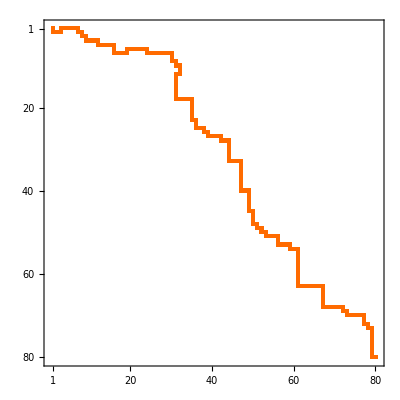

```mathematica
plotShortestPath[sum]
```